1692.46

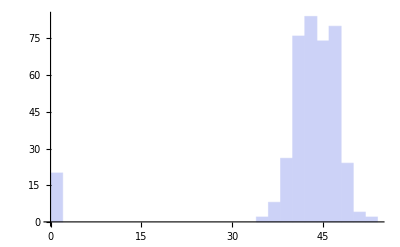

4339.74

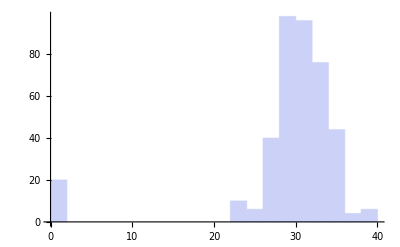

33018.2

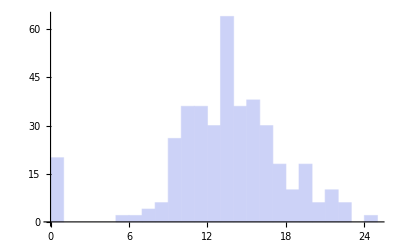

56942.4

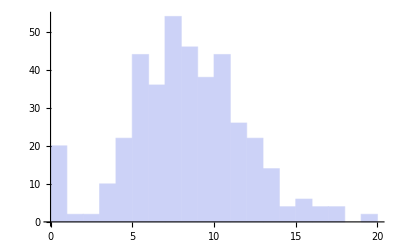

79749.

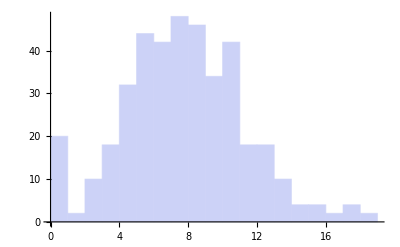

118775.

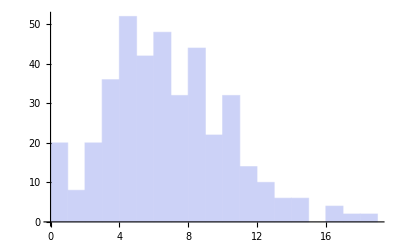

191376.

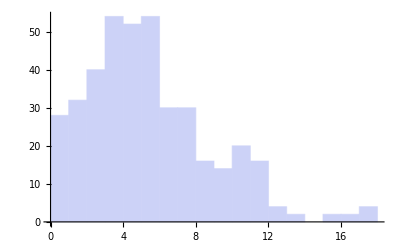

378386.

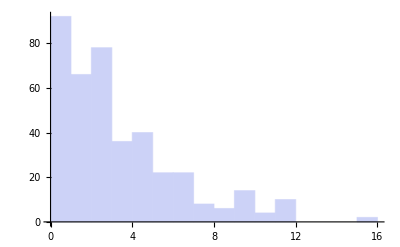

```mathematica
points=RandomVariate[NormalDistribution[0,1],{20,1000}];
For[i=1,i≤20,i++,points[[i]]=points[[i]]/Norm[points[[i]]]*100];
getDis[m_]:=Table[Norm[m[[i]]-m[[j]]],{i,1,20},{j,1,20}];
proj[d_]:=Table[If[j≤d,points[[i,j]],0],{i,1,20},{j,1,1000}];
calcError[m1_,m2_]:=Sum[((m1[[i,j]]-m2[[i,j]])/
(m1[[i,j]]+10^-20))^2,{i,1,20},{j,1,20}]
draw[m_]:=Print[Histogram[Flatten[m],20]]
Do[Print[calcError[getDis[points]*k/1000,getDis[proj[k]]]];
draw[getDis[proj[k]]],{k,{100,50,10,5,4,3,2,1}}]
```